# Machine learning on appendicitis dataset

## Import

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\juank\OneDrive\Research\Machine Learning\Appendicitis

```mathematica
data=SemanticImport["Machine learning.csv"];
```

```mathematica
data⟦;;5⟧
```

Dataset[<>]

## Manipulating the data

```mathematica
Length[data]
```

200

```mathematica
eightyPercent=Floor[0.8*Length[data]]
```

160

```mathematica
twentyPercent=Length[data]-eightyPercent
```

40

```mathematica
allRows=Table[n,{n,Length[data]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}

```mathematica
randomRows=RandomSample[Range[Length[data]],eightyPercent]
```

{68,12,180,48,174,105,53,41,169,100,42,89,94,50,54,195,120,172,6,85,197,191,1,112,91,178,22,31,10,38,79,117,76,111,32,152,4,137,125,135,192,9,56,164,140,188,52,27,115,145,72,171,126,87,173,138,3,78,157,28,151,108,16,97,123,66,139,49,128,186,159,101,118,102,67,130,80,60,190,23,103,146,93,46,200,17,199,150,88,83,124,179,133,104,109,13,142,134,119,160,110,26,147,44,81,96,113,47,99,69,158,98,95,163,114,14,148,198,167,29,39,2,161,92,170,144,185,154,75,153,33,196,82,166,8,162,156,122,129,20,18,131,168,84,189,5,19,90,36,7,86,43,182,183,107,55,63,116,127,61}

```mathematica
randomRowsSelect=Table[{randomRows⟦n⟧},{n,Length[randomRows]}]
```

{{68},{12},{180},{48},{174},{105},{53},{41},{169},{100},{42},{89},{94},{50},{54},{195},{120},{172},{6},{85},{197},{191},{1},{112},{91},{178},{22},{31},{10},{38},{79},{117},{76},{111},{32},{152},{4},{137},{125},{135},{192},{9},{56},{164},{140},{188},{52},{27},{115},{145},{72},{171},{126},{87},{173},{138},{3},{78},{157},{28},{151},{108},{16},{97},{123},{66},{139},{49},{128},{186},{159},{101},{118},{102},{67},{130},{80},{60},{190},{23},{103},{146},{93},{46},{200},{17},{199},{150},{88},{83},{124},{179},{133},{104},{109},{13},{142},{134},{119},{160},{110},{26},{147},{44},{81},{96},{113},{47},{99},{69},{158},{98},{95},{163},{114},{14},{148},{198},{167},{29},{39},{2},{161},{92},{170},{144},{185},{154},{75},{153},{33},{196},{82},{166},{8},{162},{156},{122},{129},{20},{18},{131},{168},{84},{189},{5},{19},{90},{36},{7},{86},{43},{182},{183},{107},{55},{63},{116},{127},{61}}

```mathematica
randomRowsNot=Delete[allRows,randomRowsSelect]
```

{11,15,21,24,25,30,34,35,37,40,45,51,57,58,59,62,64,65,70,71,73,74,77,106,121,132,136,141,143,149,155,165,175,176,177,181,184,187,193,194}

```mathematica
dataTrain=data⟦randomRows⟧;
dataTest=data⟦randomRowsNot⟧;
```

```mathematica
dataTestModel=Table[{dataTest⟦n,1⟧,dataTest⟦n,2⟧,dataTest⟦n,3⟧,dataTest⟦n,4⟧,dataTest⟦n,5⟧,dataTest⟦n,6⟧,dataTest⟦n,7⟧,dataTest⟦n,8⟧}->dataTest⟦n,9⟧,{n,1,Length[dataTest]}]
```

{{0,1,1,1,0,0.555556,0.904523,0.257448}→0,{0,0,1,1,1,0.833333,0.962312,0.290548}→0,{1,0,0,0,0,0.486111,0.957286,0.16918}→0,{1,0,0,1,0,0.541667,0.922111,0.364104}→0,{0,0,0,0,0,0.506944,0.942211,0.250092}→0,{0,0,0,0,0,0.5,0.919598,0.228025}→0,{0,0,0,0,0,0.527778,0.929648,0.316293}→0,{0,1,0,0,0,0.541667,0.972362,0.139757}→0,{0,0,0,1,0,0.618056,0.937186,0.37146}→0,{0,0,0,0,1,0.513889,0.91206,0.294226}→0,{0,0,1,0,0,0.548611,0.944724,0.327326}→0,{0,0,0,0,0,0.534722,0.859296,0.514895}→0,{0,1,1,0,0,0.604167,0.917085,0.290548}→0,{0,0,1,0,0,0.5625,0.904523,0.261125}→0,{0,0,1,1,0,0.569444,0.944724,0.360427}→0,{0,0,1,0,0,0.555556,0.826633,0.415594}→0,{1,1,1,0,0,0.5625,0.919598,0.426627}→0,{0,0,1,0,1,0.569444,0.929648,0.268481}→0,{0,1,0,0,0,0.569444,0.904523,0.246414}→0,{0,0,0,1,0,0.652778,0.904523,0.275837}→0,{1,0,0,0,0,0.555556,0.919598,0.28687}→0,{1,0,0,0,0,0.444444,0.982412,0.275837}→0,{0,0,1,1,0,0.631944,0.937186,0.228025}→0,{0,1,0,1,1,0.645833,0.954774,1.}→1,{1,1,1,1,1,0.520833,0.929648,0.426627}→1,{1,1,1,1,0,0.875,0.954774,0.441339}→1,{1,0,1,1,0,0.555556,0.904523,0.573005}→1,{1,0,1,1,1,0.902778,0.937186,0.492828}→1,{1,0,1,1,0,0.625,0.904523,0.532549}→1,{0,1,1,1,1,0.451389,0.904523,0.522251}→1,{0,1,1,1,1,0.5625,0.904523,0.330636}→1,{0,1,1,1,1,0.694444,0.969849,0.891504}→1,{1,1,1,1,1,0.902778,0.944724,0.474439}→1,{1,1,1,1,1,0.840278,0.964824,0.963222}→1,{1,1,1,1,1,0.944444,0.974874,0.484001}→1,{1,1,1,1,1,0.694444,0.954774,0.45605}→1,{1,1,1,1,0,0.763889,0.954774,0.44612}→1,{1,1,1,1,1,0.833333,0.954774,0.433615}→1,{0,1,0,1,1,0.763889,0.98995,0.502758}→1,{0,1,1,1,1,0.861111,0.967337,0.464509}→1}

## Random forest model

```mathematica
rfModel=Classify[dataTrain->"Histo",Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
rfModelCM=ClassifierMeasurements[rfModel,dataTestModel]
```

ClassifierMeasurementsObject[…]

```mathematica
rfModelCM["Properties"]
```

{Accuracy,AccuracyRejectionPlot,ClassRejectionRate,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,Error,FScore,InversePerplexity,Likelihood,LogLikelihood,LogLikelihoodRate,Perplexity,Precision,Properties,Recall,RejectionRate}

```mathematica
rfModelCM["Accuracy"]
```

0.925

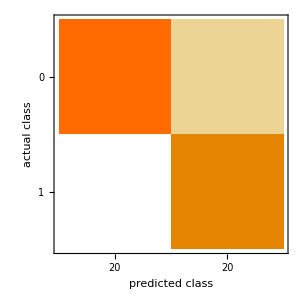

```mathematica
rfModelCM["ConfusionMatrixPlot"]
```

```mathematica
Manipulate[rfModelCM[prop],{prop,rfModelCM["Properties"]},SaveDefinitions->True]
```

## Logistic regression model

```mathematica
lrModel=Classify[dataTrain->"Histo",Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
lrModelCM=ClassifierMeasurements[lrModel,dataTestModel]
```

ClassifierMeasurementsObject[…]

```mathematica
Manipulate[lrModelCM[prop],{prop,lrModelCM["Properties"]},SaveDefinitions->True]
```

## Support vector machine model

```mathematica
svModel=Classify[dataTrain->"Histo",Method->"SupportVectorMachine"];
svModelCM=ClassifierMeasurements[svModel,dataTestModel];
```

```mathematica
Manipulate[svModelCM[prop],{prop,svModelCM["Properties"]},SaveDefinitions->True]
```

## Feature extraction

```mathematica
dataFeature=data⟦All,{1,2,3,4,5,6,7,8}⟧;
```

```mathematica
fe=FeatureExtraction[dataFeature]
```

FeatureExtractorFunction[…]

```mathematica
rfModelFE=Classify[dataTrain->"Histo",Method->"RandomForest",FeatureExtractor->fe]
```

ClassifierFunction[…]

```mathematica
rfModelFECM=ClassifierMeasurements[rfModelFE,dataTestModel]
```

ClassifierMeasurementsObject[…]

```mathematica
rfModelFECM["Accuracy"]
```

0.925